```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory["/Users/Pedro/Dropbox/Morel/mu_cases/mu_cases_0.05"]
```

/Users/Pedro/Dropbox/Morel/mu_cases/mu_cases_0.05

```mathematica
step =   10^-5;
```

Casos com y 0.05

```mathematica
μtotal5 = {};
ilist = {"20","22","24","26","28","30","32","34","36","38","40"};
jlist = {"1","2","3","4"};
For[i=0,i<11,i++;
localμ = {};
For[j=0,j<4,j++;
{iloc,jloc} = {ilist⟦i⟧,jlist⟦j⟧};
μi = Import["mu" <> jloc <> iloc <> ".txt", "Table"];
AppendTo[localμ, μi]];
AppendTo[μtotal5,localμ]];
```

```mathematica
maxlist51 = {};
listmean51= {};
minlist51 ={};
maxxlist51 ={};
For[i=0,i< Length[μtotal5],i++;
statμi = μtotal5⟦i,1,All,1⟧;
xlist = HistogramList[statμi, {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi, {0,1,step}]⟦2⟧;
AppendTo[minlist51,Min[statμi]];
AppendTo[maxxlist51,Max[statμi]];
AppendTo[maxlist51,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean51,Mean[statμi]]];
```

```mathematica
Min[statμi]
```

-0.103801

```mathematica
maxlist52 = {};
listmean52 = {};
minlist52 ={};
maxxlist52 ={};
For[i=0,i< Length[μtotal5],i++;
statμi = μtotal5⟦i,2,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[minlist52,Min[statμi]];
AppendTo[maxxlist52,Max[statμi]];
AppendTo[maxlist52,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean52,Mean[statμi]]];
```

```mathematica
maxlist53 = {};
listmean53 = {};
minlist53 ={};
maxxlist53 ={};
For[i=0,i< Length[μtotal5],i++;
statμi = μtotal5⟦i,3,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[minlist53,Min[statμi]];
AppendTo[maxxlist53,Max[statμi]];
AppendTo[maxlist53,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean53,Mean[statμi]]];
```

```mathematica
maxlist54 = {};
listmean54 = {};
For[i=0,i< Length[μtotal5],i++;
statμi = μtotal5⟦i,4,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[maxlist54,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean54,Mean[statμi]]];
```

Casos com y 0.01

```mathematica
SetDirectory["/Users/Pedro/Dropbox/Morel/mu_cases/mu_cases_0.01"]
```

/Users/Pedro/Dropbox/Morel/mu_cases/mu_cases_0.01

```mathematica
μtotal1 = {};
ilist = {"20","22","24","26","28","30","32","34","36","38","40"};
jlist = {"1","2","3","4"};
For[i=0,i<11,i++;
localμ = {};
For[j=0,j<4,j++;
{iloc,jloc} = {ilist⟦i⟧,jlist⟦j⟧};
μi = Import["mu" <> jloc <> iloc <> ".txt", "Table"];
AppendTo[localμ, μi]];
AppendTo[μtotal1,localμ]];
```

```mathematica
step =   10^-5;
```

```mathematica
maxlist11 = {};
listmean11= {};
minlist11 ={};
maxxlist11 ={};
For[i=0,i< Length[μtotal1],i++;
statμi = μtotal1⟦i,1,All,1⟧;
xlist = HistogramList[statμi, {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi, {0,1,step}]⟦2⟧;
AppendTo[minlist11,Min[statμi]];
AppendTo[maxxlist11,Max[statμi]];
AppendTo[maxlist11,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean11,Mean[statμi]]];
```

```mathematica
maxlist12 = {};
listmean12 = {};
minlist12 ={};
maxxlist12 ={};
For[i=0,i< Length[μtotal1],i++;
statμi = μtotal1⟦i,2,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[minlist12,Min[statμi]];
AppendTo[maxxlist12,Max[statμi]];
AppendTo[maxlist12,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean12,Mean[statμi]]];
```

```mathematica
maxlist13 = {};
listmean13 = {};
minlist13 ={};
maxxlist13={};
For[i=0,i< Length[μtotal1],i++;
statμi = μtotal1⟦i,3,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[minlist13,Min[statμi]];
AppendTo[maxxlist13,Max[statμi]];
AppendTo[maxlist13,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean13,Mean[statμi]]];
```

```mathematica
maxlist14 = {};
listmean14 = {};
For[i=0,i< Length[μtotal1],i++;
statμi = μtotal1⟦i,4,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[maxlist14,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean14,Mean[statμi]]];
```

```mathematica
Show[ListPlot[μtotal5⟦1,1⟧, PlotStyle->LightBlue], ListPlot[μtotal5⟦1,2⟧, PlotStyle->LightRed],ListPlot[μtotal5⟦1,3⟧, PlotStyle->LightGreen],ListPlot[μtotal5⟦1,4⟧, PlotStyle->LightPurple],ListPlot[μtotal1⟦1,1⟧, PlotStyle->Blue], ListPlot[μtotal1⟦1,2⟧, PlotStyle->Red],ListPlot[μtotal1⟦1,3⟧, PlotStyle->Green],ListPlot[μtotal1⟦1,4⟧, PlotStyle->Purple],PlotRange-> {{-0.5,2.5},{-0.08,0.08}}]
```

-Graphics-

```mathematica
Show[ListPlot[μtotal1⟦2,4⟧,PlotStyle->Black],-Graphics- ,PlotRange-> {{0.5,0.52},Automatic}]
```

-Graphics-

```mathematica
μtotal1⟦1,4,All,1⟧
```

{0.505311,0.505311,0.505311,0.512085,0.512085,0.512085,0.508199,0.508199,0.508199,29982,0.510765,0.510765,0.510765,0.506359,0.506359,0.506359,0.510306,0.510306,0.510306}
 |  |  |  |

```mathematica
Histogram[μtotal1⟦2,4⟧,{0.5,0.52,10^-5}]
```

$Aborted

```mathematica
Histogram[μtotal1⟦1,4⟧,{0.5,0.52,10^-5}]
```

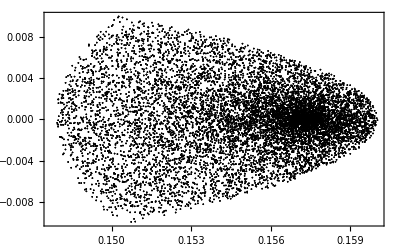

```mathematica
ListPlot[μtotal1⟦2,1⟧,PlotStyle->Black,Frame-> True]
```

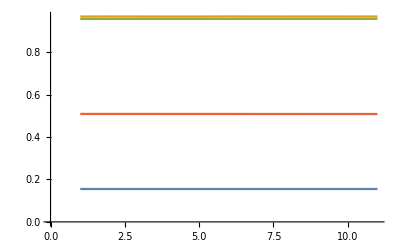

```mathematica
ListPlot[{listmean11,listmean12, listmean13, listmean14},Joined->True]
```

```mathematica
listmean11
```

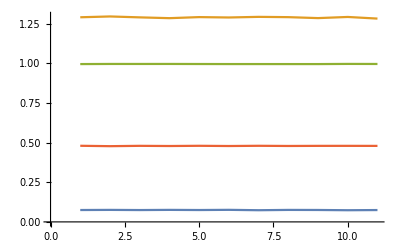

```mathematica
ListPlot[{listmean51,listmean52, listmean53, listmean54},Joined->True]
```

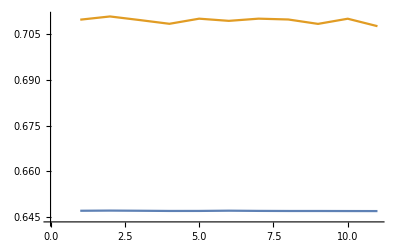

```mathematica
ListPlot[{Total[{listmean11,listmean12, listmean13, listmean14}]/4,Total[{listmean51,listmean52, listmean53, listmean54}]/4},Joined->True]
```

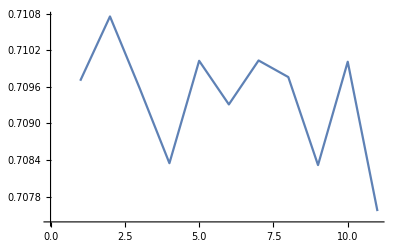

```mathematica
ListPlot[Total[{listmean51,listmean52, listmean53, listmean54}]/4,Joined->True]
```

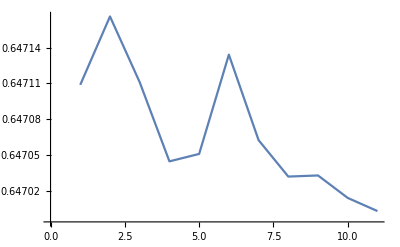

```mathematica
ListPlot[Total[{listmean11,listmean12, listmean13, listmean14}]/4,Joined->True]
```

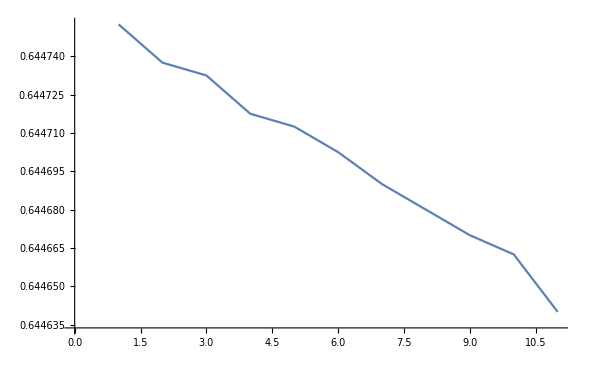

```mathematica
ListPlot[Total[{maxlist11,maxlist12, maxlist13, maxlist14}]/4,Joined->True]
```

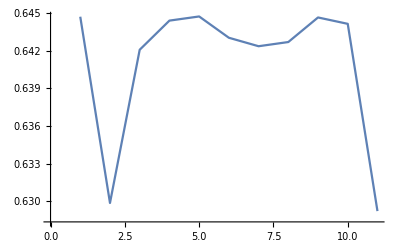

```mathematica
ListPlot[Total[{maxlist51,maxlist52, maxlist53, maxlist54}]/4,Joined->True]
```

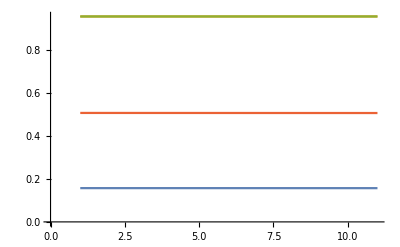

```mathematica
ListPlot[{maxlist11,maxlist12, maxlist13, maxlist14},Joined->True]
```

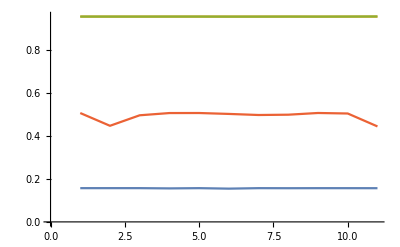

```mathematica
ListPlot[{maxlist51,maxlist52, maxlist53, maxlist54},Joined->True]
```

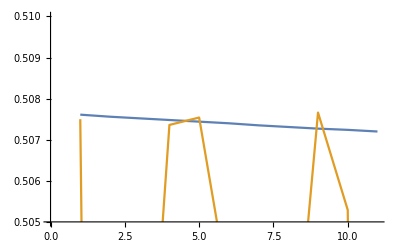

```mathematica
ListPlot[{maxlist14,maxlist54},Joined->True,PlotRange-> {0.505,0.51}]
```

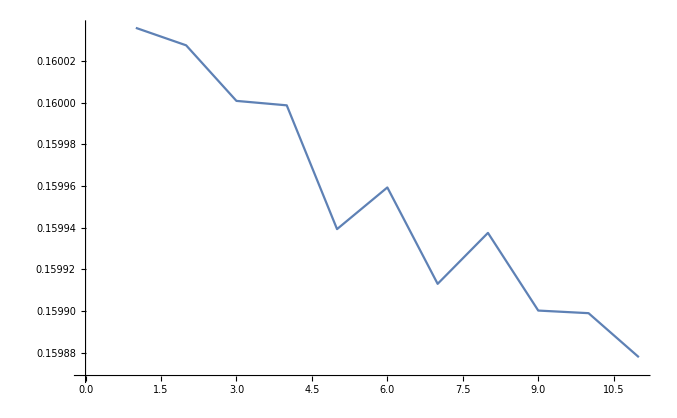

```mathematica
ListPlot[maxxlist11,Joined->True]
```

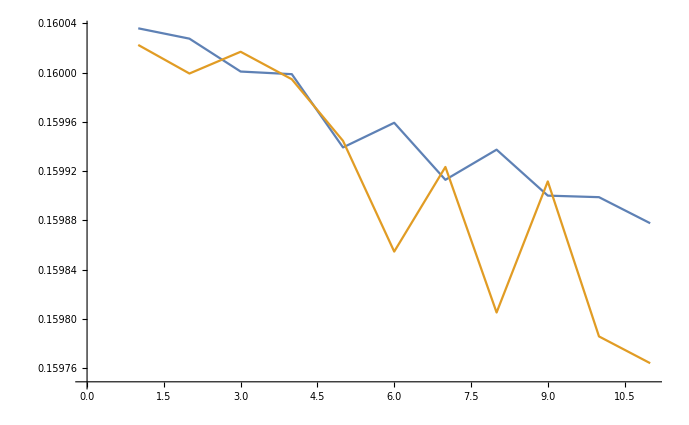

```mathematica
ListPlot[{maxxlist11,maxxlist51}, Joined->True]
```

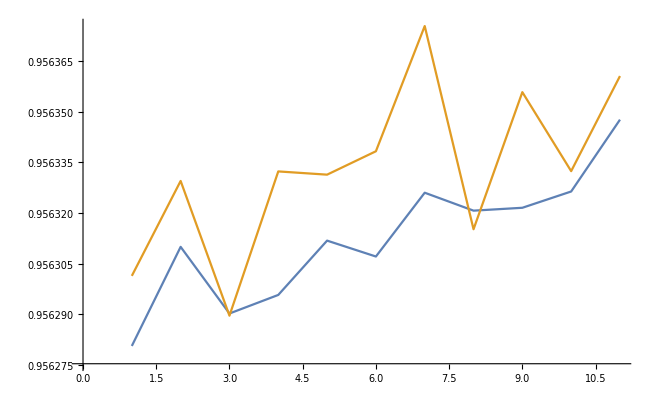

```mathematica
ListPlot[{minlist12,minlist52}, Joined->True]
```

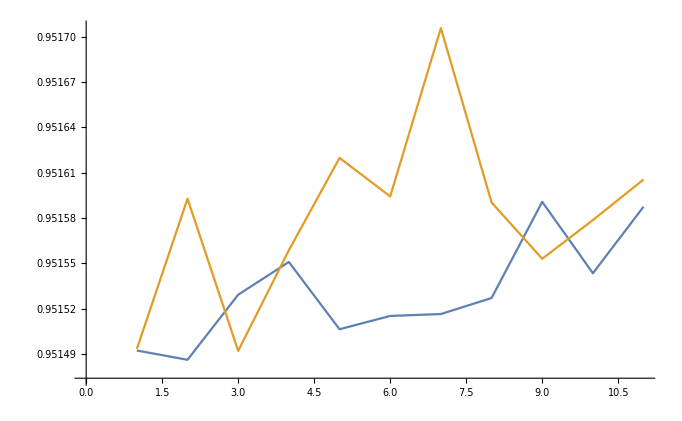

```mathematica
ListPlot[{minlist13,minlist53}, Joined->True]
```

```mathematica
ListPlot[maxlist11,Joined->True]
```

```mathematica
ListPlot[{maxlist11,maxlist51},Joined->True]
```